# Little Fingers

Brian Beckman
9 May 2019

```mathematica
t2θ=x^2/(1-x^2);1+t2θ//FullSimplify
```

1/(1-x^2)

```mathematica
Cos[ArcTan[x/(√(1-x^2))]]==√(1-x^2)//FullSimplify
```

1/(√(1/(1-x^2)))==√(1-x^2)

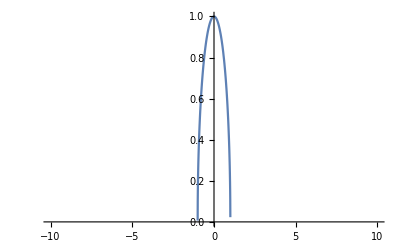

```mathematica
Plot[√(1-x^2),{x,-10,10}]
```

Fingers appear to be pendula. Let’s have stacked pendula with spherical spring-dampers, then figure out the normal modes. First a review of normal modes of oscillations

2-link, stacked pendula in 2D. MIT8_03SCF16_Text_Ch3.pdf.

Top link

l1	half-length of top link
l2	half-length of bottom link
r	radii of the links about long axis, same for the two links
θ1	swing angle from vertical downward of the top link
θ2	swing angle from vertical of bottom link
m1	mass of top link
m2	mass of bottom link

asdf

```mathematica
ClearAll[l1,l2,r,θ1,θ2,x1,y1,x2,y2,m1,m2,J1,J2]
topLink=Cylinder[{{-l1,0,0},{l1,0,0}},r];
J1=m1 MomentOfInertia[topLink,Assumptions->l1>0&&r>0]/Volume[topLink]
bottomLink=Cylinder[{{-l2,0,0},{l2,0,0}},r];
J2=m2 MomentOfInertia[bottomLink,Assumptions->l2>0&&r>0]/Volume[bottomLink]
```

{{(m1 r^2)/2,0,0},{0,(m1 (16 l1^4+12 l1^2 r^2))/(48 l1^2),0},{0,0,(m1 (16 l1^4+12 l1^2 r^2))/(48 l1^2)}}

{{(m2 r^2)/2,0,0},{0,(m2 (16 l2^4+12 l2^2 r^2))/(48 l2^2),0},{0,0,(m2 (16 l2^4+12 l2^2 r^2))/(48 l2^2)}}

1/2 m r^2 + 1/2 J

From https://stackoverflow.com/questions/4201346

```mathematica
ClearAll[approxEqual,expr1,expr2];
expr1=1/Sqrt[2] Log[Cosh[q+x/Sqrt[2]] Sech[q-x/Sqrt[2]]];
expr2=Sqrt[2] ArcTanh[Tanh[q] Tanh[x/Sqrt[2]]];

approxEqual[lhs_,rhs_,tol_: 10^-10]:=
Module[{vars=
DeleteDuplicates[
Cases[
{lhs,rhs},
s_Symbol/;Not[ValueQ[s]],
Infinity (* levelspec *)]]},
Chop[First[Quiet[
FindMaximum[
Abs[lhs-rhs],
Evaluate[Sequence@@vars]
]]],tol]==0]

approxEqual[expr1,expr2]
approxEqual[expr1,expr2,10^-20]
```

True

False

From https://mathematica.stackexchange.com/questions/51491/

```mathematica
ClearAll[polarEllipseParametric,r];
polarEllipseParametric[a_,b_,θ_,t_]:=
a (√2.)/(√(1+(a/b)^2+(1-(a/b)^2)Cos[2(t-θ)]));
```

```mathematica
data=With[{a=1,b=0.5,θ=π/3.0,x0=1,y0=1},
Table[
{x0,y0}+{Cos[t],Sin[t]}*polarEllipseParametric[a,b,θ,t]+
RandomVariate[NormalDistribution[0,.05],2],{t,RandomVariate[UniformDistribution[{0,2.π}],100]}]];
```

```mathematica
data=
Select[
With[{a=1,b=0.1,θ=π/6.,x0=1,y0=1},Table[{x0,y0}+{Cos[t],Sin[t]}*polarEllipseParametric[a,b,θ,t]+RandomVariate[NormalDistribution[0,.01],2],{t,RandomVariate[UniformDistribution[{0,2.π}],200]}]],#[[1]]>1&&#[[2]]>1/2&];
```

Spectacular failing case

```mathematica
data={{0.16550727710836116,0.07368858739595108},{0.13464824318933685,0.14954202398584215},{0.074303898354803,0.22868388471452056},{-0.032382794181396043,0.3081017058878809},{-0.21388888888888882,0.3704664227300099},{-0.4926902869387768,0.35796044659618564},{-0.7754996473179878,0.1648375386102261},{-0.7754996473179879,-0.1648375386102261},{-0.49269028693877703,-0.35796044659618564},{-0.2138888888888892,-0.37046642273000996},{-0.03238279418139636,-0.30810170588788127},{0.07430389835480296,-0.22868388471452059},{0.13464824318933685,-0.14954202398584204},{0.1655072771083609,-0.07368858739595108},{0.175,0.}};
```

```mathematica
(*data=Round[data,10.0^-2]*)
```

```mathematica
ClearAll[bestpfit,param,guess];
bestpfit[{xc_?NumericQ,yc_?NumericQ},data_]:=
Module[{polardata,fit},
polardata={ArcTan@@#,Norm[#]}&/@(#-{xc,yc}&/@data);
fit=NonlinearModelFit[
polardata,
polarEllipseParametric[a,b,θ,t],
{a,b,θ},
{t}];
Sow[fit["BestFitParameters"]];
Norm@fit["FitResiduals"]];
```

```mathematica
ClearAll[result,x0,y0,ellipseFit];
ellipseFit[data_]:=
With[{guess=Mean[data]},
Module[{
intermediate=
Reap[Quiet@
FindMinimum[
bestpfit[{x0,y0},data],
{{x0,guess⟦1⟧},{y0,guess⟦2⟧}}]],
min2,params},
params=Last@First@Last@intermediate;
min2=Last@First@intermediate;
params~Join~min2]];
```

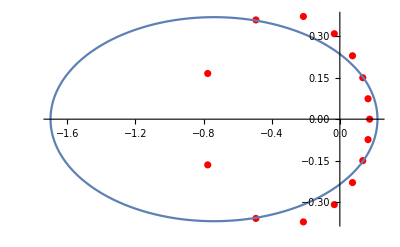

```mathematica
Show[
With[{result=ellipseFit[data]},{
ListPlot[data,PlotStyle->Red],
ParametricPlot[
{x0,y0}+
{Cos[t],Sin[t]}*
polarEllipseParametric[a,b,θ,t]/.result,
{t,0,2.π}]}],PlotRange->All]
```

```mathematica
Mean[data]
```

{-0.140334,-2.40548×10^-17}

```mathematica
newData=With[{μ=Mean[data]},(#-μ)&/@data]
```

{{0.305841,0.0736886},{0.274982,0.149542},{0.214638,0.228684},{0.107951,0.308102},{-0.0735553,0.370466},{-0.352357,0.35796},{-0.635166,0.164838},{-0.635166,-0.164838},{-0.352357,-0.35796},{-0.0735553,-0.370466},{0.107951,-0.308102},{0.214638,-0.228684},{0.274982,-0.149542},{0.305841,-0.0736886},{0.315334,2.40548×10^-17}}

```mathematica
MatrixForm/@({uu,ww,vv}=SingularValueDecomposition[newData,2])
```

{(-0.240351 | 0.0762014
-0.2161 | 0.154641
-0.168677 | 0.236482
-0.0848354 | 0.318608
0.0578049 | 0.383099
0.276907 | 0.370167
0.499158 | 0.170458
0.499158 | -0.170458
0.276907 | -0.370167
0.0578049 | -0.383099
-0.0848354 | -0.318608
-0.168677 | -0.236482
-0.2161 | -0.154641
-0.240351 | -0.0762014
-0.247811 | -4.1521×10^-17),(1.27247 | 0.
0. | 0.967025),(-1. | -1.91639×10^-16
-1.91639×10^-16 | 1.)}

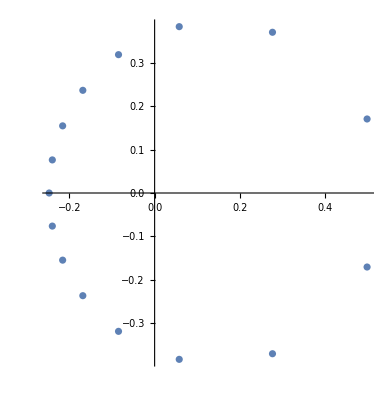

```mathematica
ListPlot[uu,AspectRatio->Automatic]
```

```mathematica
rsqr=Mean[#.#&/@uu]
```

0.133333

```mathematica
{nx,ny}=Inverse[vv.ww].({x,y}-Mean[data])
```

{-0.78587 (0.140334+x)-1.50603×10^-16 (2.40548×10^-17+y),-1.98174×10^-16 (0.140334+x)+1.0341 (2.40548×10^-17+y)}

```mathematica
expr=Expand[nx^2+ny^2]
```

0.0121626+0.173338 x+0.617592 x^2+2.71474×10^-17 y-1.73154×10^-16 x y+1.06936 y^2

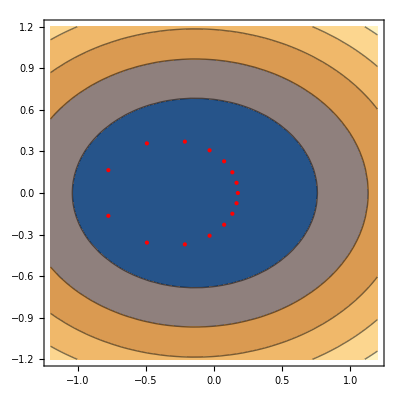

```mathematica
ContourPlot[Evaluate@expr,{x,-1.2,1.2},{y,-1.2,1.2},
Epilog->{Red,PointSize[Medium],Point[data]}]
```

```mathematica
net=NetGraph[<|"power_x"->ElementwiseLayer[#^2&],"power_y"->ElementwiseLayer[#^2&],"times_x_y"->ThreadingLayer[Times],"times_x_y_B"->ThreadingLayer[Times],"times_A_x2"->ThreadingLayer[Times],"times_C_y2"->ThreadingLayer[Times],"times_D_x"->ThreadingLayer[Times],"times_E_y"->ThreadingLayer[Times],"A"->ConstantArrayLayer["Array"->{1}],"B"->ConstantArrayLayer["Array"->{1}],"C"->ConstantArrayLayer["Array"->{1}],"D"->ConstantArrayLayer["Array"->{1}],"E"->ConstantArrayLayer["Array"->{1}],"F"->ConstantArrayLayer["Array"->{1}],"total"->TotalLayer[]|>,{NetPort["x"]->"power_x",{"power_x","A"}->"times_A_x2"->"total",NetPort["y"]->"power_y",{"power_y","C"}->"times_C_y2"->"total",{NetPort["x"],NetPort["y"]}->"times_x_y",{"times_x_y","B"}->"times_x_y_B"->"total",{"D",NetPort["x"]}->"times_D_x"->"total",{"E",NetPort["y"]}->"times_E_y"->"total","F"->"total"}]
```

NetGraph[<>]

```mathematica
nuData=<|
"x"->List/@#[[All,1]],
"y"->List/@#[[All,2]],
"Output"->List/@ConstantArray[0,Length@#]|>&@data
```

<|x→{{0.165507},{0.134648},{0.0743039},{-0.0323828},{-0.213889},{-0.49269},{-0.7755},{-0.7755},{-0.49269},{-0.213889},{-0.0323828},{0.0743039},{0.134648},{0.165507},{0.175}},y→{{0.0736886},{0.149542},{0.228684},{0.308102},{0.370466},{0.35796},{0.164838},{-0.164838},{-0.35796},{-0.370466},{-0.308102},{-0.228684},{-0.149542},{-0.0736886},{0.}},Output→{{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0}}|>

```mathematica
tnet=NetTrain[net,nuData,
MaxTrainingRounds->15000]
```

NetGraph[<>]

```mathematica
data
```

{{0.165507,0.0736886},{0.134648,0.149542},{0.0743039,0.228684},{-0.0323828,0.308102},{-0.213889,0.370466},{-0.49269,0.35796},{-0.7755,0.164838},{-0.7755,-0.164838},{-0.49269,-0.35796},{-0.213889,-0.370466},{-0.0323828,-0.308102},{0.0743039,-0.228684},{0.134648,-0.149542},{0.165507,-0.0736886},{0.175,0.}}

```mathematica
plotSolution[weightsAss_]:=Module[{t=Flatten@Values@KeySort[weightsAss]},Show[ContourPlot[
{t⟦1,1⟧*x^2+t⟦2,1⟧ x y+t⟦3,1⟧*y^2+t⟦4,1⟧ x+t⟦5,1⟧ y+t⟦6,1⟧==0},{x,-1.2,1.2},
{y,-1.2,1.2}],
ListPlot[data,PlotStyle->Red]]];

printSolution[weightsAss_]:=Module[{t=Flatten@Values@KeySort[weightsAss]},Print[t⟦1⟧*x^2+t⟦2⟧ x y+t⟦3⟧*y^2+t⟦4⟧ x+t⟦5⟧ y+t⟦6⟧==0]];

tnet=NetTrain[net,nuData,MaxTrainingRounds->15000,TrainingProgressReporting->{plotSolution[#Weights]&,"Interval"->0.1}]
```

NetGraph[<>]

```mathematica
ClearAll[convexHull];
convexHull[points_]:=
(*Needs["ComputationalGeometry`"];*)
MeshCoordinates[ConvexHullMesh[points]];
```

```mathematica
ClearAll[bounding2Ellipse];
bounding2Ellipse[PT_]:=
Module[{d=2,N,PTPrime,P,Q,count=1,err=1,u,U,tolerance=0.001,V,M,j,maximum,α,du,newU,A,c,radii},
PTPrime=DeleteDuplicates[convexHull[PT]];
N=Length[PTPrime];
P=PTPrimeᵀ;
Q=Append[P,ConstantArray[1.,N]];
u=ConstantArray[1./N,N];
While[err>tolerance,
V=Q.DiagonalMatrix[u].Qᵀ;
M=Diagonal[Qᵀ.Inverse[V].Q];
maximum=Max[M];
j=Position[M,maximum,2]⟦1,1⟧;(* discrete argmax *)
α=(maximum-d-1)/((d+1)*(maximum-1));
newU=(1-α)*u;
newU[[j]]+=α;
err=Norm[newU-u];
count++;
u=newU];
U=DiagonalMatrix[u];
c=Partition[P.u,1];
A=d(P.U.Pᵀ-c.cᵀ);
{Flatten@c,A}]
```

```mathematica
ClearAll[errorEllipsoid];
errorEllipsoid[pos_,cov_]:=
Module[{u,w,v ,θ,evs},
{u,w,v}=SingularValueDecomposition[cov];
θ=ArcTan[v⟦1,1⟧,v⟦1,2⟧];
evs=Sqrt/@Diagonal[w];
Rotate[Circle[pos,evs],θ]];
```

```mathematica
Graphics[errorEllipsoid@@bounding2Ellipse[data]]
```

-Graphics-

```mathematica
ClearAll[points,pairwise,closeList,perpProjectedPointAndParameter,perpRenderable,yForXFromLine,lineLineIntersection,print];
points=n↦Table[{Cos[(2.π i)/n],Sin[(2.π i)/n]},{i,n}];
pairwise[fxy_,l_List]:=MapThread[fxy,{Drop[l,-1],Drop[l,1]}];
closeList[l_List]:=Join[l,{First[l]}];
print=Null&;
perpProjectedPointAndParameter[p_,{u_,v_}]:=
Module[{l,q,t},
l=v-u;
t=((p-u).l)/(l.l);
q=u+t l;
{q,t}]
perpRenderable[p0_,dir:{p1_,p2_},scale_:4]:=
Module[{dx,dy,dq},
{dx,dy}=p2-p1;
dq={-dy,dx};
{p0-scale*dq,p0+scale*dq}];
yForXFromLine[x_Symbol,{p1_,p2_}]:=
Module[{dx,dy,m,b,b1},
print[<|"p1"->p1,"p2"->p2|>];
{dx,dy}=p2-p1;
m=dy/dx;(*If[dx≠0,dy/dx,Infinity];*)
b=p1⟦2⟧-m*p1⟦1⟧;
b1=p2⟦2⟧-m*p2⟦1⟧;
Assert[approxEqual[b, b1]];
print[<|"b"->b,"m"->m,"b1"->b1|>];
m x+b];
lineLineIntersection[l1:{p11_,p21_},l2:{p12_,p22_}]:=
(print[<|"l1"->l1,"l2"->l2|>];
Module[{x,y4x1,y4x2,theX,yf1,yf2},
y4x1=yForXFromLine[x,l1];
y4x2=yForXFromLine[x,l2];
theX=Solve[y4x1==y4x2,x]⟦1,1,2⟧;
yf1=y4x1/.x->theX;
yf2=y4x2/.x->theX;
Assert[approxEqual[yf1,yf2]];
{theX,yf1}]);
With[{o={0,0}},
DynamicModule[{votoggle=True},
Manipulate[
Module[{pts=points[n],vees,vperps,operps,orbrds,sects,oscts,hues,arrows},
hues=Hue[#/n]&/@Range[n];
arrows=MapIndexed[{p,is}↦{Hue[is⟦1⟧/n],Arrow[{star,p}]},pts];
Show[{
Graphics[{
Point/@pts,
LightRed,pairwise[Arrow[{#1,#2}]&,closeList@pts],
LightBlue,Arrow[{o,#}]&/@pts,
arrows,
(*LightGray,Arrow[{star,#}]&/@pts,*)
If[votoggle,
{vperps=perpRenderable[(#+star)/(2/s),{star,#}]&/@pts;
operps={o,#}&/@pts;
sects=MapThread[lineLineIntersection,{vperps,operps}];
MapIndexed[{l,is}↦{Hue[is⟦1⟧/n],Line@l},vperps],
(*LightGray,Line/@vperps,*)
Red,Point/@sects,
Red,pairwise[Line@*List,closeList@sects],
Green,errorEllipsoid@@bounding2Ellipse[sects]},
{vees={star,#}&/@pts;
orbrds=perpRenderable[#/(2/s),{o,#}]&/@pts;
oscts=MapThread[lineLineIntersection,{vees,orbrds}];
LightBlue,Line/@orbrds,
Purple,Point/@oscts,
Magenta,errorEllipsoid@@bounding2Ellipse[oscts]}]
},PlotRange->1.15 s,ImageSize->Large]  }]  ],
{{star,{-0.65,0.001}},Locator},
Control[Button["Click Here",votoggle=Not[votoggle]]],
{{s,1},0.5,4,Appearance->"Labeled"},
{{n,6},4,32,1,Appearance->"Labeled"}]]]
```

```mathematica
ExportStylesheet::usage="ExportStylesheet[fn]\nExports the private stylesheet of the current notebook to some other one designated by fn. If the notebook designated by fn was open before, one would loose unstored edits. To prevent this, the target notebook is saved automatically before closing it.";
ExportStylesheet[fn_]:=
Module[{nbk},
nbk=NotebookOpen[fn];
If[nbk==$Failed,
Print["ImportStylesheet: Wrong Filename: ",fn];
Throw["Wrong filename!"]  (* ===THROW===>*)];
SetOptions[nbk,Options[EvaluationNotebook[],StyleDefinitions]];
NotebookSave[nbk];(*safeguard against edit losses*)
NotebookClose[nbk];(*closes without asking to store*)
];(*ExportStylesheet*)
```

```mathematica
ExportStylesheet["/home/ANT.AMAZON.COM/bbeckman/Dropbox/DOLPHIN/PENDULUM/LittleFiingers_n.nb"]
```